```mathematica
(*  cell dehydration -  Dehydration by phase change at a temperature below T phw -  temp1 *)
(*  See Smith et al. JBME 1998 *)

d=21.2;
(*µm*)
mol=0;
vb=.39;
(*non-dimensional non solvent volume *)
b=5;
(* cooling rates C/min *)
lpg=1.83;
(*µm/min-atm*)
elp=100;
(* kcal/mole *)
r=1.986;
(*  gas constant - unit 1 *)
r2=82.06 10^12;
(*  gas constant - unit 2 *)
hf=5.95 10^16;
(*heat of fusion - kJ / mole *)
vw=18.136 10^12;
(*  micron^3/mole *)
vs=27 10^12;
(*  micron^3/mole *)
vdmso=71.28 10^12;
(*  micron^3/mole *)
vo=4/3 3.1415927 (d/2)^3;
(*  µm^3  *)
ao= 4* 3.1415927 (d/2)^2;
(*  µm^2  *)
vb=vb vo;
(*  conversion to volume   *)
elp=elp 1000;
(*  unit conversion  *)
ns=(.285 (vo-vb))/10^15;
(*  moles   *)
ncpa=(mol (vo-vb))/10^15;
(*  moles   *)
tr=273.15;
(*  temperature K  *)
temp1 = 271.476
(*  temperature K  *)
temp2 = 272
(*  temperature K  *)

sol=NDSolve[{v'[t]==-1/vw((lpg * ao * r2 *277) (Log[(v[t]-vb-ncpa vdmso)/(v[t]-vb-ncpa vdmso+vw (ns+ncpa))]-(hf (1/tr-1/temp1))/r2)),v[0]==vo},{v},{t,20}]
```

271.476

272

{{v→InterpolatingFunction[{{0.,20.}},<>]}}

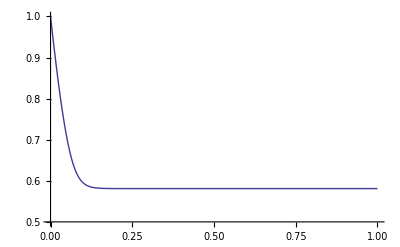

```mathematica
p6=Plot[Evaluate[{v[t]}/.sol]/vo,{t,0,1},PlotRange->{0.5,1}]
```

```mathematica
Show[p1,p2,p3, p4, p5, p6, PlotRange -> {0,1}]
```

⁃Graphics⁃

```mathematica
(*  Krogh cylinder  -  Dehydration during phase change at a cooling rate after nucleation at Tr - *)

rv=3.8;
dx=22;
l=12.7;
vo=((dx^2)-(3.1415927*rv^2))*l
(*  Volume is a cylinder, not a sphere as above *)
mol=0;
vb=.35;
b=.1;
lpg=1.9;
elp=69;
r=1.986;
r2=82.06 10^12;
hf=5.95 10^16;
vw=18.136 10^12;
vs=27 10^12;
vdmso=71.28 10^12;

vb=vb vo;
elp=elp 1000;
ns=(.285 (vo-vb))/10^15;
ncpa=(mol (vo-vb))/10^15;
tr=273.15;
lp[t_]:=lpg 2.718^(-(elp (1/(273.15-t)-1/tr))/r)
lp[.53];
sol=NDSolve[{v'[t]==-1/(vw b)((lp[t] 2 3.1415927 rv l r2 (273.15-t)) (Log[(v[t]-vb-ncpa vdmso)/(v[t]-vb-ncpa vdmso+vw (ns+ncpa))]-(hf (1/tr-1/(273.15-t)))/r2)),v[.53]==vo},{v},{t,20}]
```

5570.67

{{v→InterpolatingFunction[{{0.53,20.}},<>]}}

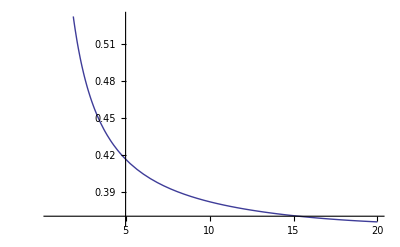

```mathematica
peq=Plot[Evaluate[{v[t]}/.sol]/vo,{t,0.53,20}]
```

```mathematica
Show[peq, p01,p05,p10, p20]
```

⁃Graphics⁃